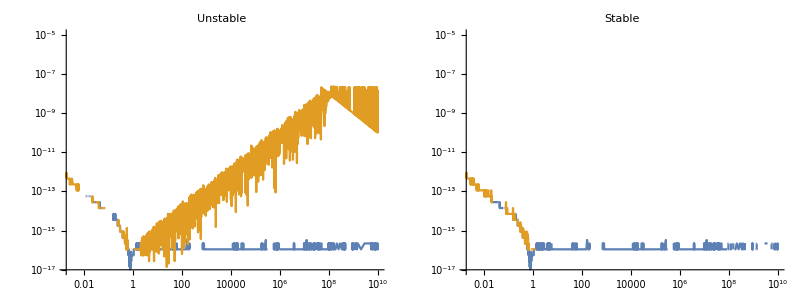

```mathematica
sinphi[b_,r_]:=(1-r^2-b^2)/(2 b r);
cosphi[b_,r_]:=√(1-sinphi[b,r]^2);
sinphistable[b_,r_]:=(1-r^2-b^2)/(2 b r);
cosphistable[b_,r_]:=Module[{ϵ=((1-(b-r)) (1+(b-r)))/(2 b r)},√(2ϵ-ϵ^2)];
{{
LogLogPlot[{
Abs[sinphi[Max[0.1,r-0.1],r]-sinphi[SetAccuracy[Max[0.1,r-0.1],40],SetAccuracy[r,40]]],
Abs[cosphi[Max[0.1,r-0.1],r]-cosphi[SetAccuracy[Max[0.1,r-0.1],40],SetAccuracy[r,40]]]
},{r,10^-3,10^10},PlotLabel->"Unstable",ImageSize->Medium,PlotRange->{10^-17,10^-5}],
LogLogPlot[{
Abs[sinphistable[Max[0.1,r-0.1],r]-sinphi[SetAccuracy[Max[0.1,r-0.1],40],SetAccuracy[r,40]]],
Abs[cosphistable[Max[0.1,r-0.1],r]-cosphi[SetAccuracy[Max[0.1,r-0.1],40],SetAccuracy[r,40]]]
},{r,10^-3,10^10},PlotLabel->"Stable",ImageSize->Medium,PlotRange->{10^-17,10^-5}]
}}//TableForm
```

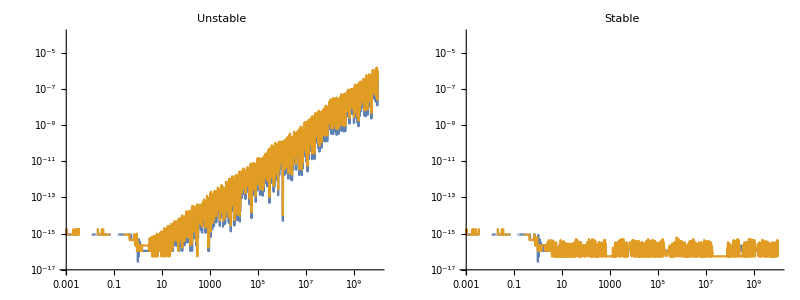

```mathematica
sinlam[b_,r_]:=(1+b^2-r^2)/(2 b);
coslam[b_,r_]:=√(1-sinlam[b,r]^2);
sinlamstable[b_,r_]:=(1+(b+r)(b-r))/(2 b);
coslamstable[b_,r_]:=√(1-sinlamstable[b,r]^2);
{{
LogLogPlot[{
Abs[sinlam[Max[0.1,r-0.9],r]-sinlam[SetAccuracy[Max[0.1,r-0.9],40],SetAccuracy[r,40]]],
Abs[coslam[Max[0.1,r-0.9],r]-coslam[SetAccuracy[Max[0.1,r-0.9],40],SetAccuracy[r,40]]]
},{r,10^-3,10^10},PlotLabel->"Unstable",ImageSize->Medium,PlotRange->{10^-17,10^-4}],
LogLogPlot[{
Abs[sinlamstable[Max[0.1,r-0.9],r]-sinlam[SetAccuracy[Max[0.1,r-0.9],40],SetAccuracy[r,40]]],
Abs[coslamstable[Max[0.1,r-0.9],r]-coslam[SetAccuracy[Max[0.1,r-0.9],40],SetAccuracy[r,40]]]
},{r,10^-3,10^10},PlotLabel->"Stable",ImageSize->Medium,PlotRange->{10^-17,10^-4}]
}}//TableForm
```